# Sympathetic cooling with 1 ion

```mathematica
ClearAll["Global`*"]
```

## Parameters

### Physics and known system parameters

```mathematica
hbar=1.05*10^(-34);
eps0=8.85*10^(-12);
kB=1.38*10^(-23);

(*Paul trap parameters*)
(*in x-driection*)
dx=0.9*10^(-3);αx=0.93;
V0x=-0.5*V0z*(αz/αx)*(dx/dz)^2;
Vslowx=80;Vfastx=1350;
(*in y-driection*)
dy=0.9*10^(-3);αy=0.93;
V0y=-0.5*V0z*(αz/αy)*(dy/dz)^2;
Vslowy=-80;Vfasty=-1350;
(*in z-driection*)
dz=1.7*10^(-3);αz=0.38;
V0z=56.5;
Vslowz=0;Vfastz=0;

ωslow=2Pi*7*10^(3);ωfast=2Pi*17.5*10^(6);
l=ωslow/ωfast;

(*Ion parameters*)
Qi = 1.6*10^(-19);Mi=40*1.6*10^(-27);
(*Nanoparticle parameters*)
Rp=133.5*10^(-9);
Mp=2*10^(-17);Qp=750*Qi;


(*Mathieu parameters*)
(*for the ion*)
axi=(4*Qi*V0x*αx)/(Mi*ωfast^2*dx^2);qslowxi=(2*Qi*Vslowx*αx)/(Mi*ωslow^2*dx^2);qfastxi=(2*Qi*Vfastx*αx)/(Mi*ωfast^2*dx^2);
ayi=(4*Qi*V0y*αy)/(Mi*ωfast^2*dy^2);qslowyi=(2*Qi*Vslowy*αy)/(Mi*ωslow^2*dy^2);qfastyi=(2*Qi*Vfasty*αy)/(Mi*ωfast^2*dy^2);
azi=(4*Qi*V0z*αz)/(Mi*ωfast^2*dz^2);qslowzi=(4*Qi*Vslowz*αz)/(Mi*ωslow^2*dz^2);qfastzi=(4*Qi*Vfastz*αz)/(Mi*ωfast^2*dz^2);
(*for the nanoparticle*)
axp=(4*Qp*V0x*αx)/(Mp*ωfast^2*dx^2);qslowxp=(2*Qp*Vslowx*αx)/(Mp*ωslow^2*dx^2);qfastxp=(2*Qp*Vfastx*αx)/(Mp*ωfast^2*dx^2);
ayp=(4*Qp*V0y*αy)/(Mp*ωfast^2*dy^2);qslowyp=(2*Qp*Vslowy*αy)/(Mp*ωslow^2*dy^2);qfastyp=(2*Qp*Vfasty*αy)/(Mp*ωfast^2*dy^2);
azp=(4*Qp*V0z*αz)/(Mp*ωfast^2*dz^2);qslowzp=(4*Qp*Vslowz*αz)/(Mp*ωslow^2*dz^2);qfastzp=(4*Qp*Vfastz*αz)/(Mp*ωfast^2*dz^2);
```

### Effective secular trap frequencies

```mathematica
(*for the ion*)
Ωxi=1/(√2)((ωfast/2 √(axi+qfastxi^2/2))^2+ωslow^2/4+√(((ωfast/2 √(axi+qfastxi^2/2))^2-ωslow^2/4)^2-(qslowxi^2*ωslow^4)/8))^(1/2);
Ωyi=1/(√2)((ωfast/2 √(ayi+qfastyi^2/2))^2+ωslow^2/4+√(((ωfast/2 √(ayi+qfastyi^2/2))^2-ωslow^2/4)^2-(qslowyi^2*ωslow^4)/8))^(1/2);
Ωzi=1/(√2)((ωfast/2 √(azi+qfastzi^2/2))^2+ωslow^2/4+√(((ωfast/2 √(azi+qfastzi^2/2))^2-ωslow^2/4)^2-(qslowzi^2*ωslow^4)/8))^(1/2);

(*for the nanoparticle*)
Ωxp=ωfast/2 √(axp+(qslowyp^2*l^2)/2+qfastxp^2/2);
Ωyp=ωfast/2 √(ayp+(qslowxp^2*l^2)/2+qfastyp^2/2);
Ωzp=ωfast/2 √(azp+(qslowzp^2*l^2)/2+qfastzp^2/2);
```

### Distance between ion and nanoparticle

```mathematica
d=((Qi*Qp)/(4*Pi*eps0)*(1/(Mi*Ωzi^2)+1/(Mp*Ωzp^2)))^(1/3);
```

### Trap frequency renormalisations

```mathematica
(*for the ion*)
(*in x-driection*)
newΩxi=Sqrt[Ωxi^2-(Qi*Qp)/(4*Pi*eps0*Mi*d^3)];
xzpfi=Sqrt[hbar/(2*Mi*newΩxi)];
(*in y-driection*)
newΩyi=Sqrt[Ωyi^2-(Qi*Qp)/(4*Pi*eps0*Mi*d^3)];
yzpfi=Sqrt[hbar/(2*Mi*newΩyi)];
(*in z-driection*)
newΩzi=Sqrt[Ωzi^2+2*(Qi*Qp)/(4*Pi*eps0*Mi*d^3)];
zzpfi=Sqrt[hbar/(2*Mi*newΩzi)];

(*for the nanoparticle*)
(*in x-driection*)
newΩxp=Sqrt[Ωxp^2-(Qi*Qp)/(4*Pi*eps0*Mp*d^3)];
xzpfp=Sqrt[hbar/(2*Mp*newΩxp)];
(*in y-driection*)
newΩyp=Sqrt[Ωyp^2-(Qi*Qp)/(4*Pi*eps0*Mp*d^3)];
yzpfp=Sqrt[hbar/(2*Mp*newΩyp)];
(*in z-driection*)
newΩzp=Sqrt[Ωzp^2+2*(Qi*Qp)/(4*Pi*eps0*Mp*d^3)];
zzpfp=Sqrt[hbar/(2*Mp*newΩzp)];
```

### Couplings

```mathematica
gx=+1/hbar*(Qi*Qp)/(4*Pi*eps0)*(xzpfi*xzpfp)/d^3;
gy=+1/hbar*(Qi*Qp)/(4*Pi*eps0)*(yzpfi*yzpfp)/d^3;
gz=-1/hbar*(Qi*Qp)/(2*Pi*eps0)*(zzpfi*zzpfp)/d^3;
```

### Γ_ba/γ_fb values

```mathematica
Γtoγz=842.08;(*in x-driection*)
Γtoγx=561.39;(*in y-driection*)
Γtoγy=750.09;(*in z-driection*)
```

### Choose axis for computation

```mathematica
(*Choose the axis along which the nanoparticle COM motion accupation number is to be plotted*)
gip=gx;
newΩp=newΩxp;
newΩi=newΩxi;
Γtoγ=Γtoγx;
```

### Dissipators

```mathematica
(*for the ion*)
(*This is the Doppler heating rate Γ_dop*)
Edoti=3.8*10^(-22);Γi=Edoti/(hbar*newΩi);
(*This is the Doppler damping rate γ_dop*)
γi=2*Pi*10*10^(3);

(*for the nanoparticle*)
(*This is the gas heating rate Γ_gas*)
ΓGasDamping[R_,M_,P_,T_]:=(kB*T)/(hbar*newΩp)*γGasDamping[R,M,P,T];
ΓpGasDamping=ΓGasDamping[Rp,Mp,1*10^(-8),300];
(*This is the back action heating rate Γ_ba*)
ΓpFeedback[γp_]:=Γtoγ*(γp-γp1);
(*This is the trap displacement heating rate Γ_td*)
EdotpTrapDisp=2.8*10^(-26);ΓpTrapDisp=EdotpTrapDisp/(hbar*newΩp);
(*This is the gas damping rate γ_gas*)
γGasDamping[R_,M_,P_,T_]:=0.619*((6*Pi*R^2)/M)*P*Sqrt[(2*m0)/(Pi*kB*T)]/.{m0->((28*10^(-3))/(6.022*10^(23)))};
γp1=γGasDamping[Rp,Mp,1*10^(-8),300];
(*This is the typical damping rate from feedback cooling*)
γp2=2*Pi*1*10^(0);
```

## Equations of motion of the system

```mathematica
(*We define the equations of motion matrices as functions of the total nanoparticle damping rate and the trap displacement heating rate, since these are the two parameters that we'll vary in the following plots*)

(*Equations of motion for second order moments of ladder operators*)
(*v_q=[b_p^\dagger b_p, b_p^\dagger b_i, b_i^\dagger b_p, b_i^\dagger b_i, b_p^\dagger b_p^\dagger, b_p^\dagger, b_i^\dagger, b_i^\dagger b_i^\dagger, b_p b_p, b_p b_i, b_i b_i]*)
(*This is the drift matrix for second order moments*)
fMQ[γp_,Γtd_]:=ReplaceAll[{Ω1->newΩp,Γh1->ΓpGasDamping,Γc1->ΓpGasDamping+γp,Ω2->newΩi,Γh2->Γi,Γc2->Γi+γi,g12->gip,Γfb->ΓpFeedback[γp]}][{
{1/2 (-2 Γc1+2 Γh1),-ⅈ g12,ⅈ g12,0,0,-ⅈ g12,0,0,ⅈ g12,0},
{-ⅈ g12,1/2 (-Γc1-Γc2+Γh1+Γh2)+ⅈ (Ω1-Ω2),0,ⅈ g12,-ⅈ g12,0,0,0,0,ⅈ g12},{ⅈ g12,0,1/2 (-Γc1-Γc2+Γh1+Γh2)+ⅈ (-Ω1+Ω2),-ⅈ g12,0,0,-ⅈ g12,ⅈ g12,0,0},
{0,ⅈ g12,-ⅈ g12,1/2 (-2 Γc2+2 Γh2),0,-ⅈ g12,0,0,ⅈ g12,0},
{0,2 ⅈ g12,0,0,1/2 (-2 Γc1+2 Γh1)+2 ⅈ Ω1,2 ⅈ g12,0,0,0,0},
{ⅈ g12,0,0,ⅈ g12,ⅈ g12,1/2 (-Γc1-Γc2+Γh1+Γh2)+ⅈ (Ω1+Ω2),ⅈ g12,0,0,0},
{0,0,2 ⅈ g12,0,0,2 ⅈ g12,1/2 (-2 Γc2+2 Γh2)+2 ⅈ Ω2,0,0,0},
{0,0,-2 ⅈ g12,0,0,0,0,1/2 (-2 Γc1+2 Γh1)-2 ⅈ Ω1,-2 ⅈ g12,0},{-ⅈ g12,0,0,-ⅈ g12,0,0,0,-ⅈ g12,1/2 (-Γc1-Γc2+Γh1+Γh2)-ⅈ (Ω1+Ω2),-ⅈ g12},{0,-2 ⅈ g12,0,0,0,0,0,0,-2 ⅈ g12,1/2 (-2 Γc2+2 Γh2)-2 ⅈ Ω2}
}];

(*This is the diffusion vector for second order moments*)
fAvec[γp_,Γtd_]:=ReplaceAll[{Ω1->newΩp,Γh1->ΓpGasDamping,Γc1->ΓpGasDamping+γp,Ω2->newΩi,Γh2->Γi,Γc2->Γi+γi,g12->gip,Γfb->ΓpFeedback[γp]}][{
Γh1+Γfb+Γtd,0,0,Γh2,-Γfb-Γtd,ⅈ g12,0,-Γfb-Γtd,-ⅈ g12,0
}];

(*Equations of motion for first order moments of ladder operators*)
(*v_s=[b_p, b_i, b_p^\dagger, b_i^\dagger]*)
(*This is the drift matrix for first order moments*)
fMS[γp_,Γtd_]:=ReplaceAll[{Ω1->newΩp,Γh1->ΓpGasDamping,Γc1->ΓpGasDamping+γp,Ω2->newΩi,Γh2->Γi,Γc2->Γi+γi,g12->gip,Γfb->ΓpFeedback[γp]}][{
{1/2 (-Γc1+Γh1)-ⅈ Ω1,-ⅈ g12,0,-ⅈ g12},
{-ⅈ g12,1/2 (-Γc2+Γh2)-ⅈ Ω2,-ⅈ g12,0},
{0,ⅈ g12,1/2 (-Γc1+Γh1)+ⅈ Ω1,ⅈ g12},
{ⅈ g12,0,ⅈ g12,1/2 (-Γc2+Γh2)+ⅈ Ω2}
}];
```

## Plots

### Nanoparticle COM motion occupation vs damping rate

```mathematica
(*We define an array of nanoparticle damping rates over which we wish to compute the nanoparticle COM occupation*) 
γptab=Insert[2Pi*PowerRange[10^(-7),10^(3),10^(1/30)],γp1,1];
(*We compute the drift and diffusion matrices of the second moments for the different nanoparticle damping rates in the array*) 
MQtabSmall=Table[fMQ[γp,0],{γp,γptab}];
AvectabSmall=Table[fAvec[γp,0],{γp,γptab}];
MQtabLarge=Table[fMQ[γp,ΓpTrapDisp],{γp,γptab}];
AvectabLarge=Table[fAvec[γp,ΓpTrapDisp],{γp,γptab}];

(*We compute the steady state values of the second order moments for each damping rate by setting the derivative of the second moments to zero and solving the linear system of equations*)
sstabSmall=Table[LinearSolve[MQtabSmall[[i]],-1*AvectabSmall[[i]]],{i,1,Length[MQtabSmall]}];
sstabLarge=Table[LinearSolve[MQtabLarge[[i]],-1*AvectabLarge[[i]]],{i,1,Length[MQtabLarge]}];
(*We extract the nanoparticle COM motion occupation*)
npsstabSmall=sstabSmall[[All,1]];
npsstabLarge=sstabLarge[[All,1]];
(*We extract the ion motion occupation*)
nisstabSmall=sstabSmall[[All,4]];
nisstabLarge=sstabLarge[[All,4]];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-2.78018×10^-7+0. ⅈ,0.-1057.58 ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ},{0.-1057.58 ⅈ,-31415.9-2.45069×10^7 ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ},«7»,{0.+0. ⅈ,0.-2115.15 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-2115.15 ⅈ,-62831.9-4.90339×10^7 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-6.28319×10^-7+0. ⅈ,0.-1057.58 ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ},{0.-1057.58 ⅈ,-31415.9-2.45069×10^7 ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ},«7»,{0.+0. ⅈ,0.-2115.15 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-2115.15 ⅈ,-62831.9-4.90339×10^7 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-6.78443×10^-7+0. ⅈ,0.-1057.58 ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ},{0.-1057.58 ⅈ,-31415.9-2.45069×10^7 ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ},«7»,{0.+0. ⅈ,0.-2115.15 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-2115.15 ⅈ,-62831.9-4.90339×10^7 ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-2.78018×10^-7+0. ⅈ,0.-1057.58 ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ},{0.-1057.58 ⅈ,-31415.9-2.45069×10^7 ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ},«7»,{0.+0. ⅈ,0.-2115.15 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-2115.15 ⅈ,-62831.9-4.90339×10^7 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-6.28319×10^-7+0. ⅈ,0.-1057.58 ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ},{0.-1057.58 ⅈ,-31415.9-2.45069×10^7 ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ},«7»,{0.+0. ⅈ,0.-2115.15 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-2115.15 ⅈ,-62831.9-4.90339×10^7 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-6.78443×10^-7+0. ⅈ,0.-1057.58 ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.+0. ⅈ},{0.-1057.58 ⅈ,-31415.9-2.45069×10^7 ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ,0.-1057.58 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+1057.58 ⅈ},«7»,{0.+0. ⅈ,0.-2115.15 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-2115.15 ⅈ,-62831.9-4.90339×10^7 ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

### Plot

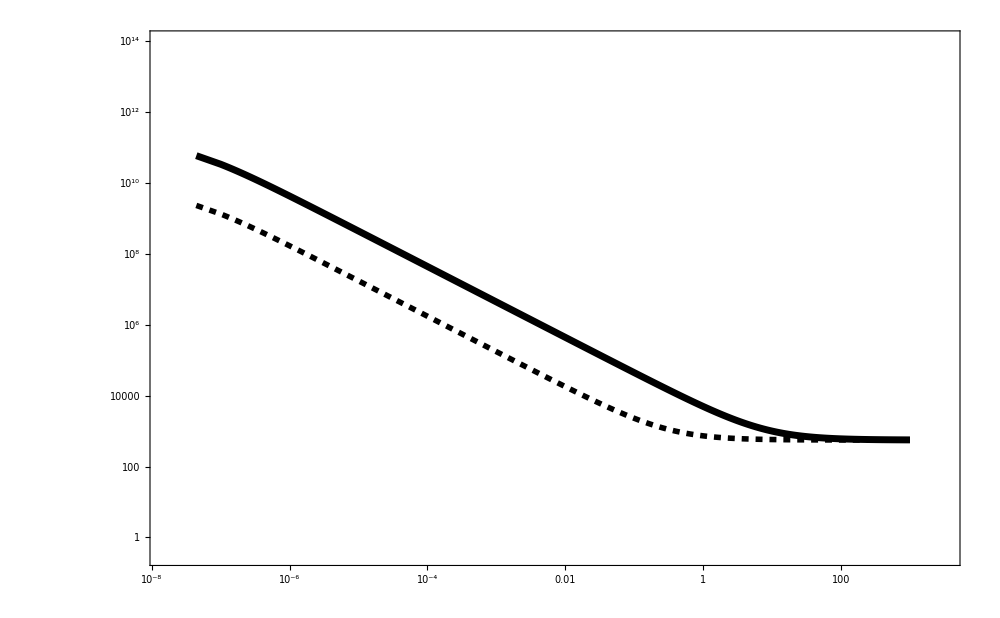

```mathematica
xmyTicks=Table[{10^i,Superscript[10,i]},{i,-10,5,3}];
ymyTicks=Table[{10^i,Superscript[10,i]},{i,-4,14,2}];

ListLogLogPlot[
{TemporalData[Re[npsstabLarge],{γptab/(2Pi)}],
TemporalData[Re[npsstabSmall],{γptab/(2Pi)}]
},
Joined->True,
PlotStyle->{
{Black,Thickness[0.005]},
{Black,Dashing[{0.005,0.005}],Thickness[0.004]}
},
PlotMarkers->{
None,
None
},
PlotRange->{{10^(-7.8),10^(3.5)},{10^(-0.5),10^(14)}},
ImageSize->1000,
GridLines->Automatic,
GridLinesStyle->Directive[GrayLevel[0.85], AbsoluteThickness[2.5]],
Frame->True,
Axes->False,
FrameStyle->Directive[Black,Thickness[0.0025],FontSize->20],
FrameTicks->{{ymyTicks,None},{xmyTicks,None}}
]
```

### Nanoparticle COM motion occupation vs heating rate

```mathematica
(*We define an array of trap displacement heating rates over which we wish to compute the nanoparticle COM occupation*) 
EdotpTrapDisptab=PowerRange[10^(-30),10^(-20),10^(1/20)];ΓpTrapDisptab=EdotpTrapDisptab/(hbar*newΩp);ΓpTrapDisptabScaled=ΓpTrapDisptab/(2Pi);
(*We compute the plots for two values of nanoparticle damping rate - only gas damping and typical feedback damping*)
γptab={γp1,γp2}//N;
(*We compute the drift and diffusion matrices of the second moments for the different nanoparticle damping and heating rates in the array*) 
MQtab=Table[fMQ[γp,Γtd],{γp,γptab},{Γtd,ΓpTrapDisptab}];
Avectab=Table[fAvec[γp,Γtd],{γp,γptab},{Γtd,ΓpTrapDisptab}];
(*We compute the steady state values of the second order moments for each heating rate and damping rate by setting the derivative of the second moments to zero and solving the linear system of equations*)
sstab=MapThread[LinearSolve,{MQtab,-1*Avectab},2];
(*We extract the nanoparticle COM motion occupation*)
npssSympathetic=sstab[[1,All,1]];
npssFeedback=sstab[[2,All,1]];
```

### Plot

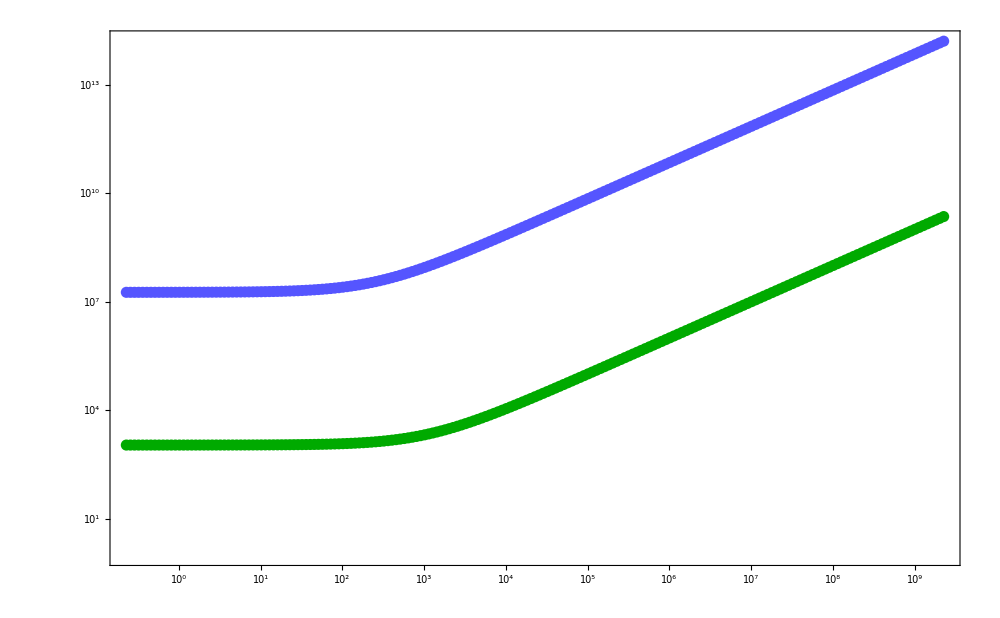

```mathematica
xmyTicks=Table[{i,Superscript[10,i],{0.01,0}},{i,-1,10,1}];
ymyTicks=Table[{j,Superscript[10,j],{0.01,0}},{j,1,18,3}];
ListPlot[
{Transpose[{Log10[ΓpTrapDisptab/(2 Pi)],Log10[Re[npssSympathetic]]}],Transpose[{Log10[ΓpTrapDisptab/(2 Pi)],Log10[Re[npssFeedback]]}]},
Frame->True,
FrameTicks->{xmyTicks,ymyTicks},
PlotStyle->{
{Lighter[Blue],PointSize[0.008],Joined->True},
{Darker[Green],PointSize[0.008],Joined->True}
},
FrameStyle->Directive[Black,Thickness[0.004],FontSize->20],
ImageSize->1000]
```